# Hydrogen Spectrum & intensity

## the incident light has uniform intensity of wavelenght, polarization. that can excite the hydrogen in any level.

```mathematica
(* Hamiltonian *)
H = Ho+ HRel+HSO+H(external Field (* For Zeeman effect *))
```

```mathematica
(* Commom Operator *)
Momemtum[f_]:= ⅈ ℏ D[f,r]
Lsquare[Y_]:=-(1/Sin[θ] D[Sin[θ]D[Y,θ],θ]+1/((Sin^2)[θ])D[Y,{ϕ,2}])
Lx[Y_]:=-ⅈ(-Sin[ϕ]D[Y,θ]- Cos[ϕ] Cot[θ]D[Y,ϕ])
Ly[Y_]:=-ⅈ(Cos[ϕ]D[Y,θ]-Cot[θ] Sin[ϕ]D[Y,ϕ])
Lz[Y_]:=-ⅈ D[Y,ϕ]
SpheMomemtum[f_]:=1/r^2 D[r^2 D[f,r],r]-1/r^2 Lsquare[f]
Ho[f_]:=-ℏ^2/(2me)SpheMomemtum[f]-e^2/(4 π ϵ r)f
wavelength[energy_]:=(2π ℏ c)/energy 1/e 10^9 (* in nm *)
```

```mathematica
(* Time -independent Perturbation *)
(* define expectation value of Hamiltonian *)
expect[ψf_,H_,ψi_]:=Integrate[ComplexExpand[Conjugate[ψf]]Composition[H][ψi] r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
(* The energy shift *)
DE[n_,H_,λ_]:= λ expect[n,H,n]+λ^2(Sum[expect[n,H,k]/(Eo[n]-Eo[k]),{k,1,n-1}]+Sum[expect[n,H,k]/(Eo[n]-Eo[k]),{k,n+1,∞}])
```

```mathematica
(* Constant *)
ℏ=6.626068×10^-34/(2π)(* m^2 kg/s *);
me=9.10938188×10^-31 (* kg *);
e = 1.60217646×10^-19 ;
ϵ=8.854187817×10^-12 (* F / me *);
c=299792458;
Z=1;
```

```mathematica
(* combinated constant *)
α = e^2/(4 π ϵ) 1/(ℏ c);
a = (4 π ϵ ℏ^2)/(me e^2);
```

```mathematica
Clear[ℏ,me,e,ϵ,a,c,α]
```

## Spectrum of Bohr Model

```mathematica
(* Solution of Hydrogen in Bohr model *)
Y[l_,m_]:= SphericalHarmonicY[l,m,θ,ϕ]
R[n_,l_,a]:=√((2/(n a))^3((n-l-1)!)/(2 n(n+l)!))Exp[-r/(n a)](2 r/(n a))^l LaguerreL[n-l-1,2l+1,2 r/(n a)]
ψ[n_,l_,m_]:=R[n,l,a]Y[l,m]
```

```mathematica
(* Ground State *)
expect[ψ[1,0,0],Ho,ψ[1,0,0]] 1/e
(* 1st excited state *)
expect[ψ[2,1,0],Ho,ψ[2,1,0]] 1/e
```

-13.6057

-3.40142

### Energy Level

{-13.6057,-3.40142,-1.51174,-0.850356,-0.544228,-0.377936}

{{{2,1},{3,1},{4,1},{5,1},{6,1}},{{3,2},{4,2},{5,2},{6,2}}}

{{121.502,102.518,97.2018,94.9236,93.7303},{656.112,486.009,433.937,410.07}}

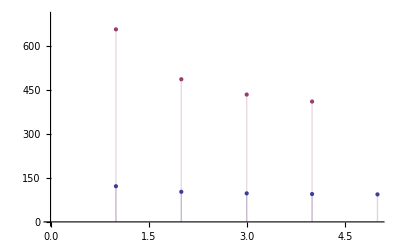

```mathematica
(* Possible energy *)
Eo[n_]:=-1/2 me c^2 α^2 1/n^2 1/e
Table[Eo[i],{i,1,6}]
Tran=Table[{i,j},{j,1,2},{i,j+1,6}]
wavelengthtable=Table[wavelength[Eo[i]-Eo[j]],{j,1,2},{i,j+1,6}]
ListPlot[%,Filling->Axis,PlotRange->{0,700}]
```

```mathematica
Table[6(i-1)+j-((i-2)(i-1))/2,{i,1,4},{j,1,7-i}]
```

{{1,2,3,4,5,6},{7,8,9,10,11},{12,13,14,15},{16,17,18}}

```mathematica
(* Listing Function *)
Listing[K_,KK_]:=Table[KK[5(i-1)+j-((i-2)(i-1))/2]=K[[i]][[j]],{i,1,2},{j,1,6-i}]
```

```mathematica
Listing[wavelengthtable,wavelengthList];
Table[wavelengthList[i],{i,1,9}]//TableForm
```

121.502
102.518
97.2018
94.9236
93.7303
656.112
486.009
433.937
410.07

```mathematica
Clear[wavelengthtable, wavelengthList]
```

### Intensity

```mathematica
(* According to the fermi Golden Rule *)
(* Transition Pobability *)
P[f_,i_]:= (2π)/ℏ expect[f ,H,i]^2 ρ[f]
(* H is the Hamitonian do the  perturbation *)
(* ρ[f] is the density of state of final state *) 
(* since the selection rule are built-in, the density of state just sum up *)
```

#### The Hamitonian is the radiation dipole

```mathematica
Hdipole=e r.electric field = e r  er. polarization
```

```mathematica
er= {Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
```

```mathematica
(* Recalled that the SPeherical Harmonic *)
Y[1,-1]
Y[1,0]
Y[1,1]
```

1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) Sin[θ]

1/2 √(3/π) Cos[θ]

1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]

```mathematica
(* we can construct the er component with Y[1,m] *)
Y[1,1]+Y[1,-1]//ExpToTrig
Y[1,1]-Y[1,-1]//ExpToTrig
Y[1,0]
```

√(3/(2 π)) Cos[ϕ] Sin[θ]

ⅈ √(3/(2 π)) Sin[θ] Sin[ϕ]

1/2 √(3/π) Cos[θ]

```mathematica
(* The er can be rewriten as *)
Collect[√((2π)/3)(A1+A3)x-ⅈ √((2π)/3)(A1-A3)y+√((4π)/3)A2 z,{A1,A2,A3}]
```

A1 (√((2 π)/3) x-ⅈ √((2 π)/3) y)+A3 (√((2 π)/3) x+ⅈ √((2 π)/3) y)+2 A2 √(π/3) z

```mathematica
er = 2 √(π/3)Y[1,1] ((x-ⅈ y)/(√2))+ 2 Y[1,0] √(π/3) z+2 √(π/3)Y[1,-1] ((x+ⅈ y)/(√2))
```

```mathematica
(* The polarization can be writen as *)
```

```mathematica
Polarization =σPulse ((x+ⅈ y)/(√2))+Pie z + σMinus((x-ⅈ y)/(√2))
```

```mathematica
er. polarization =  2 √(π/3)Y[1,1] σPulse + 2 Y[1,0] √(π/3) Pie +   2 √(π/3)Y[1,-1] σMinus
```

```mathematica
Hdipole[ψ_]:=( 2 √(π/3)e r ( Y[1,1] σPulse + Y[1,0]Pie + Y[1,-1] σMinus )ψ)/.{σPulse->1,Pie->1, σMinus->1}
```

```mathematica
expect[f,Hdipole, i]=  2 √(π/3)e ∫SuperStar[Rf] r Ri r^2 ⅆr ∫∫SuperStar[Yf] Y[1,1]  Yi Sin[θ]ⅆθⅆϕ∫∫SuperStar[Yf]  Y[1,0]Yi Sin[θ]ⅆθⅆϕ∫∫SuperStar[Yf]  Y[1,-1]  Yi Sin[θ]ⅆθⅆϕ
= Radial (σPulse Subscript[δ, 1,l] δ_□) Pie σMinus
```

```mathematica
(* test *)
Table[{{l,m},expect[ψ[1,0,0],Hdipole ,ψ[2,l,m]]},{l,0,1},{m,-l,l,1} ]
```

{{{{0,0},0}},{{{1,-1},6.31582×10^-30},{{1,0},6.31582×10^-30},{{1,1},6.31582×10^-30}}}

```mathematica
Table[{{l,m},expect[ψ[2,0,0],Hdipole ,ψ[2,l,m]]},{l,0,1},{m,-l,l,1} ]
```

{{{{0,0},0}},{{{1,-1},-2.54351×10^-29},{{1,0},-2.54351×10^-29},{{1,1},-2.54351×10^-29}}}

```mathematica
Table[{{l,m},expect[ψ[2,0,0],Hdipole, ψ[3,l,m]]},{l,0,2},{m,-l,l,1} ]
```

{{{{0,0},0}},{{{1,-1},1.50022×10^-29},{{1,0},1.50022×10^-29},{{1,1},1.50022×10^-29}},{{{2,-2},0},{{2,-1},0},{{2,0},0},{{2,1},0},{{2,2},0}}}

```mathematica
Table[{{l,m},expect[ψ[2,1,0],Hdipole ,ψ[3,l,m]]},{l,0,2},{m,-l,l,1} ]
```

{{{{0,0},4.59347×10^-30}},{{{1,-1},0},{{1,0},0},{{1,1},0}},{{{2,-2},0},{{2,-1},1.80026×10^-29},{{2,0},3.11815×10^-29},{{2,1},1.80026×10^-29},{{2,2},0}}}

```mathematica
Table[{{l,m},expect[ψ[2,1,1],Hdipole, ψ[3,l,m]]},{l,0,2},{m,-l,l,1} ]
```

{{{{0,0},4.59347×10^-30+0. ⅈ}},{{{1,-1},0},{{1,0},0},{{1,1},0}},{{{2,-2},0.+0. ⅈ},{{2,-1},0.+0. ⅈ},{{2,0},1.03938×10^-29+0. ⅈ},{{2,1},1.80026×10^-29+0. ⅈ},{{2,2},2.54596×10^-29+0. ⅈ}}}

#### Calculation

```mathematica
Pindiviual[nf_,lf_,mf_, ni_,li_,mi_]:=(2π)/ℏ Norm[expect[ψ[nf,lf,mf],Hdipole ,ψ[ni,li,mi] ]]^2 2
P[nf_, ni_]:=Sum[Pindiviual[nf,lf,mf, ni,li,mi],{lf,0,nf-1,1},{mf,-lf,lf,1},{li,0,ni-1,1},{mi,-li,li,1}]
```

```mathematica
Table[√Pindiviual[2,0,0,3,li,mi] √(ℏ/(4π)),{li,0,2},{mi,-li,li,1}]
```

{{0},{1.50022×10^-29,1.50022×10^-29,1.50022×10^-29},{0,0,0,0,0}}

```mathematica
Table[√Pindiviual[1,0,0,2,li,mi] √(ℏ/(4π)),{li,0,1},{mi,-li,li,1}]
```

{{0},{6.31582×10^-30,6.31582×10^-30,6.31582×10^-30}}

```mathematica
Table[Pindiviual[1,0,0,2,li,mi] ,{li,0,1},{mi,-li,li,1}]
```

{{0},{4.75329×10^-24,4.75329×10^-24,4.75329×10^-24}}

```mathematica
P[1,2]
P[1,3]
P[1,4]
P[1,5]
P[1,6]
P[2,3]
P[2,4]
P[2,5]
P[2,6]
```

1.42599×10^-23

2.28673×10^-24

8.17007×10^-25

3.90166×10^-25

2.17798×10^-25

5.38561×10^-22

1.21726×10^-22

5.1086×10^-23

2.70272×10^-23

```mathematica
Intensity={1.425985943400345*^-23,2.2867329066797917*^-24,8.170072530514043*^-25,3.901657406755574*^-25, 2.1779805847307437*^-25,5.385607938737635*^-22, 1.2172586364953318*^-22, 5.1086028290773386*^-23, 2.7027223572359645*^-23}
```

{1.42599×10^-23,2.28673×10^-24,8.17007×10^-25,3.90166×10^-25,2.17798×10^-25,5.38561×10^-22,1.21726×10^-22,5.1086×10^-23,2.70272×10^-23}

```mathematica
Intensity=Intensity/Max[Intensity]
```

{0.0264777,0.00424601,0.00151702,0.00072446,0.000404408,1.,0.226021,0.0948566,0.0501842}

### Spectrum

```mathematica
Clear[Spectrum]
```

```mathematica
Spectrum= Table[{wavelengthList[i],Intensity[[i]]},{i,1,9}];
Spectrum//TableForm
```

121.502 | 0.0264777
102.518 | 0.00424601
97.2018 | 0.00151702
94.9236 | 0.00072446
93.7303 | 0.000404408
656.112 | 1.
486.009 | 0.226021
433.937 | 0.0948566
410.07 | 0.0501842

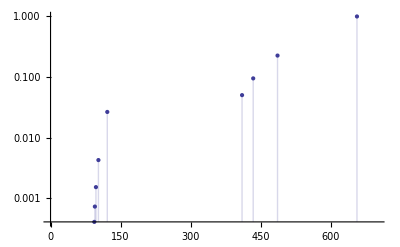

```mathematica
ListLogPlot[Spectrum,Filling->Axis,PlotRange->{{0,700},{0,0.5}}]
```

## Zeeman Effect in Bohr Model

```mathematica
(* Bohr Megneton *)
μb = (e ℏ)/(2 me);
```

```mathematica
Clear[μb]
```

```mathematica
(*The Zeeman Effect add an additional term in Hamiltonian *)
```

```mathematica
Hzee=-μ.B = - ((- e)/(2 me)L).B = m (e ℏ)/(2 me)B = m μb B
```

```mathematica
Hzee[m_,ψ_]:= m μb ψ;
```

```mathematica
(* treat it as a pertubation *)
(* first order correction is *)
DE1Hzee[n_,l_,m_,B_]:=B expect[ψ[n,l,m],Hzee[m],ψ[n,l,m]]
(* Obviously, Hzee is a constant regard of ψ, Thus, *)
DE1Hzee[n_,l_,m_,B_]:=B μb m 1/e
```

```mathematica
Table[{Eo[n],DE1Hzee[n,l,m,B]},{n,1,6},{l,0,n-1,1},{m,-l,l,1}]//TableForm
```

-13.6057 | 0 |  |  |  |  | 
-3.40142 | 0 | -3.40142 | -0.0000578838 B
-3.40142 | 0
-3.40142 | 0.0000578838 B |  |  |  | 
-1.51174 | 0 | -1.51174 | -0.0000578838 B
-1.51174 | 0
-1.51174 | 0.0000578838 B | -1.51174 | -0.000115768 B
-1.51174 | -0.0000578838 B
-1.51174 | 0
-1.51174 | 0.0000578838 B
-1.51174 | 0.000115768 B |  |  | 
-0.850356 | 0 | -0.850356 | -0.0000578838 B
-0.850356 | 0
-0.850356 | 0.0000578838 B | -0.850356 | -0.000115768 B
-0.850356 | -0.0000578838 B
-0.850356 | 0
-0.850356 | 0.0000578838 B
-0.850356 | 0.000115768 B | -0.850356 | -0.000173651 B
-0.850356 | -0.000115768 B
-0.850356 | -0.0000578838 B
-0.850356 | 0
-0.850356 | 0.0000578838 B
-0.850356 | 0.000115768 B
-0.850356 | 0.000173651 B |  | 
-0.544228 | 0 | -0.544228 | -0.0000578838 B
-0.544228 | 0
-0.544228 | 0.0000578838 B | -0.544228 | -0.000115768 B
-0.544228 | -0.0000578838 B
-0.544228 | 0
-0.544228 | 0.0000578838 B
-0.544228 | 0.000115768 B | -0.544228 | -0.000173651 B
-0.544228 | -0.000115768 B
-0.544228 | -0.0000578838 B
-0.544228 | 0
-0.544228 | 0.0000578838 B
-0.544228 | 0.000115768 B
-0.544228 | 0.000173651 B | -0.544228 | -0.000231535 B
-0.544228 | -0.000173651 B
-0.544228 | -0.000115768 B
-0.544228 | -0.0000578838 B
-0.544228 | 0
-0.544228 | 0.0000578838 B
-0.544228 | 0.000115768 B
-0.544228 | 0.000173651 B
-0.544228 | 0.000231535 B | 
-0.377936 | 0 | -0.377936 | -0.0000578838 B
-0.377936 | 0
-0.377936 | 0.0000578838 B | -0.377936 | -0.000115768 B
-0.377936 | -0.0000578838 B
-0.377936 | 0
-0.377936 | 0.0000578838 B
-0.377936 | 0.000115768 B | -0.377936 | -0.000173651 B
-0.377936 | -0.000115768 B
-0.377936 | -0.0000578838 B
-0.377936 | 0
-0.377936 | 0.0000578838 B
-0.377936 | 0.000115768 B
-0.377936 | 0.000173651 B | -0.377936 | -0.000231535 B
-0.377936 | -0.000173651 B
-0.377936 | -0.000115768 B
-0.377936 | -0.0000578838 B
-0.377936 | 0
-0.377936 | 0.0000578838 B
-0.377936 | 0.000115768 B
-0.377936 | 0.000173651 B
-0.377936 | 0.000231535 B | -0.377936 | -0.000289419 B
-0.377936 | -0.000231535 B
-0.377936 | -0.000173651 B
-0.377936 | -0.000115768 B
-0.377936 | -0.0000578838 B
-0.377936 | 0
-0.377936 | 0.0000578838 B
-0.377936 | 0.000115768 B
-0.377936 | 0.000173651 B
-0.377936 | 0.000231535 B
-0.377936 | 0.000289419 B

```mathematica
Table[{{{ni,li,mi},{nf,lf,mf}},{wavelength[(Eo[ni]+DE1Hzee[ni,li,mi,1])-(Eo[nf]+DE1Hzee[nf,lf,mf,1])]}},{nf,0,2},{lf,0,nf-1,1},{mf,-lf,lf,1},{ni,nf+1,3},{li,0,ni-1,1},{mi,-li,li,1}]//TableForm
```

| 
2
0
0 | 1
0
0
121.502 |  |  | 
2
1
-1 | 1
0
0
121.503 |  | 2
1
0 | 1
0
0
121.502 |  | 2
1
1 | 1
0
0
121.502 |  | 3
0
0 | 1
0
0
102.518 |  |  |  |  | 
3
1
-1 | 1
0
0
102.518 |  | 3
1
0 | 1
0
0
102.518 |  | 3
1
1 | 1
0
0
102.517 |  |  | 
3
2
-2 | 1
0
0
102.518 |  | 3
2
-1 | 1
0
0
102.518 |  | 3
2
0 | 1
0
0
102.518 |  | 3
2
1 | 1
0
0
102.517 |  | 3
2
2 | 1
0
0
102.517 |  | 
3
0
0 | 2
0
0
656.112 |  |  |  |  | 
3
1
-1 | 2
0
0
656.132 |  | 3
1
0 | 2
0
0
656.112 |  | 3
1
1 | 2
0
0
656.092 |  |  | 
3
2
-2 | 2
0
0
656.152 |  | 3
2
-1 | 2
0
0
656.132 |  | 3
2
0 | 2
0
0
656.112 |  | 3
2
1 | 2
0
0
656.092 |  | 3
2
2 | 2
0
0
656.072 |  | 3
0
0 | 2
1
-1
656.092 |  |  |  |  | 
3
1
-1 | 2
1
-1
656.112 |  | 3
1
0 | 2
1
-1
656.092 |  | 3
1
1 | 2
1
-1
656.072 |  |  | 
3
2
-2 | 2
1
-1
656.132 |  | 3
2
-1 | 2
1
-1
656.112 |  | 3
2
0 | 2
1
-1
656.092 |  | 3
2
1 | 2
1
-1
656.072 |  | 3
2
2 | 2
1
-1
656.052 | 
3
0
0 | 2
1
0
656.112 |  |  |  |  | 
3
1
-1 | 2
1
0
656.132 |  | 3
1
0 | 2
1
0
656.112 |  | 3
1
1 | 2
1
0
656.092 |  |  | 
3
2
-2 | 2
1
0
656.152 |  | 3
2
-1 | 2
1
0
656.132 |  | 3
2
0 | 2
1
0
656.112 |  | 3
2
1 | 2
1
0
656.092 |  | 3
2
2 | 2
1
0
656.072 | 
3
0
0 | 2
1
1
656.132 |  |  |  |  | 
3
1
-1 | 2
1
1
656.152 |  | 3
1
0 | 2
1
1
656.132 |  | 3
1
1 | 2
1
1
656.112 |  |  | 
3
2
-2 | 2
1
1
656.172 |  | 3
2
-1 | 2
1
1
656.152 |  | 3
2
0 | 2
1
1
656.132 |  | 3
2
1 | 2
1
1
656.112 |  | 3
2
2 | 2
1
1
656.092 |

```mathematica
wavelengthtable=Table[wavelength[(Eo[ni]+DE1Hzee[ni,li,mi,1])-(Eo[nf]+DE1Hzee[nf,lf,mf,1])],{nf,0,2},{lf,0,nf-1,1},{mf,-lf,lf,1},{ni,nf+1,3},{li,0,ni-1,1},{mi,-li,li,1}]
```

{{},{{{{{121.502},{121.503,121.502,121.502}},{{102.518},{102.518,102.518,102.517},{102.518,102.518,102.518,102.517,102.517}}}}},{{{{{656.112},{656.132,656.112,656.092},{656.152,656.132,656.112,656.092,656.072}}}},{{{{656.092},{656.112,656.092,656.072},{656.132,656.112,656.092,656.072,656.052}}},{{{656.112},{656.132,656.112,656.092},{656.152,656.132,656.112,656.092,656.072}}},{{{656.132},{656.152,656.132,656.112},{656.172,656.152,656.132,656.112,656.092}}}}}}

## Fine Structure Spin - Orbital

```mathematica
(* Fine Structure Spin-Orbital *)
MeanRcube[n_,l_]:=(*Integrate[1/r^3 R[n,l]^2 r^2,{r,0,∞}], For l ≠ 0 *)  1/(l(l+1/2)(1+l))(Z/(n a))^3
SLcoupling[l_,s_,j_]:=1/2(j(j+1)-l(l+1)-s(s+1))
Hso[f_,l_,s_,j_]:= ℏ^2/(2 me^2 c^2)e^2/(4π ϵ) 1/r^3 SLcoupling[l,s,j]f (* sl only act on Y and the intrice spin , Thus, s.l = 1/2(j^2-l^2-s^2) *)
DE1Hso[n_,l_,m_] := expect[ψ[n,l,m],Hso,[ψ[n,l,m],l,1/2,l+1/2]] (* First order correction *)
```

```mathematica
Composition[Sin,Cos][x,y]
```

Cos::argx: Cos called with 2 arguments; 1 argument is expected.

Sin[Cos[x,y]]

```mathematica
Table[{l,j,SLcoupling[l,1/2,j]},{l,0,3},{j,l-1/2,l+1/2,1}]//MatrixForm
```

((0
-1/2
-1/2) | (0
1/2
0)
(1
1/2
-1) | (1
3/2
1/2)
(2
3/2
-3/2) | (2
5/2
1)
(3
5/2
-2) | (3
7/2
3/2))

## Dirac

```mathematica
(* Dirac *)
ERel[n_,l_]:=(* - P^4/(8 me^3 c^2)  =*) -ℏ^4/(8 me^3 c^2)Integrate[R[n,l]D[R[n,l],{r,4}] r^2,{r,0,∞}] 1/e
ED[n_,l_,s_,j_]:=Eo[n]+Eso[n,l,s,j]+ERel[n,l]
```